积分学（Calculus)

CH1: 黎曼积分图
	Manipulate/Plot[]/DiscretePlot[]/Show[]

```mathematica
Manipulate[
	Show[{
	Plot[Sin[x],{x,0,2Pi}],
	DiscretePlot[Sin[x],{x,0,2Pi,dx},ExtentSize->Full,ColorFunction->"Rainbow"]
}],{dx,1,0.01}
]
```

```mathematica
Clear[x,y]
```

```mathematica
Manipulate[
	DiscretePlot3D[
	Sin[x+y],{x,0,2Pi,dx},
{y,0,2Pi,dx},ExtentSize->Full,ColorFunction->"Rainbow"
],{dx,1,0.1}
]
```

CH2 参数方程积分
	D[] Integrate[] NIntegrate[]

```mathematica
D[Sin[x],{x,5}] #阶导5
```

Cos[x]

```mathematica
Integrate[Sin[x],{x,0,Pi}] #定积分
```

2

```mathematica
NIntegrate[Sin[x],{x,0,Pi}] #.#isfloat
```

2.

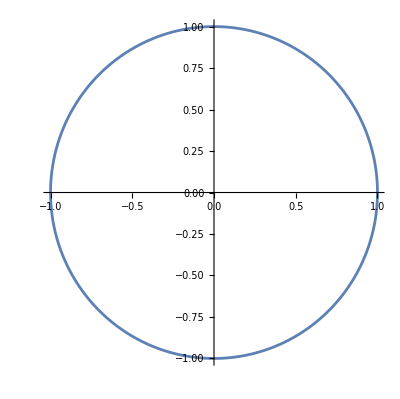

```mathematica
ParametricPlot[{
Cos[t],Sin[t]
},{t,0,2Pi}
]
```

```mathematica
#ctrlplus4islatex
```

```mathematica
Integrate[Sin[t]Cos'[t],{t,0,2Pi}]
```

-π

```mathematica
https://www.bilibili.com/cheese/play/ss22529?csource=private_space_class_null&spm_id_from=333.1387.0.0https://www.bilibili.com/cheese/play/ss22529?csource=private_space_class_null&spm_id_from=333.1387.0.0Nonehttps://www.bilibili.com/cheese/play/ss22529?csource=private_space_class_null&spm_id_from=333.1387.0.0HyperlinkActionRecycledHyperlinkActive
```

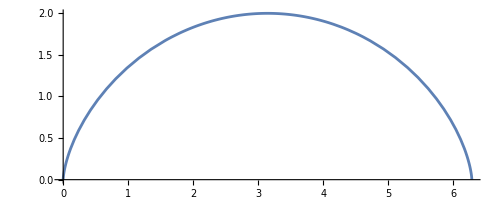

```mathematica
ParametricPlot[{
t-Sin[t],1-Cos[t]
},{t,0,2Pi}]
```

```mathematica
Integrate[(1 - Cos[t])*D[t - Sin[t], {t}], 
  {t, 0, 2*Pi}]
```

3 π

CH3: 区域积分
	试求由和2x所构成封闭区域面积

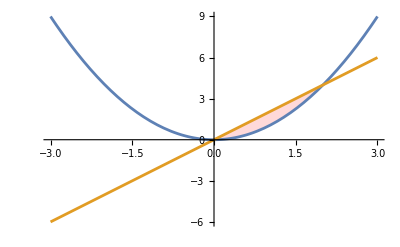

```mathematica
Plot[{x^2,2x},{x,-3,3},
Filling->{1->{{2},{LightRed,None}}}
]
```

```mathematica
Integrate[2x-x^2,{x,0,2}]
```

4/3

```mathematica
r1 = Circle[]
```

Circle[{0,0}]

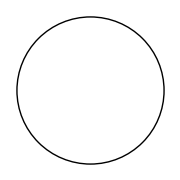

```mathematica
Graphics[r1,ImageSize->Small]
```

```mathematica
Integrate[1,{x,y}∈ r1] #escpluselement
```

Element+2 π #esc

```mathematica
r2=Disk[]
```

Disk[{0,0}]

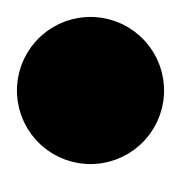

```mathematica
Graphics[r2,ImageSize->Small]
```

```mathematica
Integrate[1,{x,y}∈r2]
```

π

```mathematica
r3=ImplicitRegion[x^2<=y<=2x,{x,y}]
```

```mathematica
ImplicitRegion[x^2≤y≤2 x,{x,y}]
RegionPlot[r3,ImageSize->Small]
```

ImplicitRegion[x^2≤y≤2 x,{x,y}]

-Graphics-

```mathematica
Integrate[1,{x,y}∈r3]
```

4/3

CH4: 二重积分的面积解释
		试求由和2x所构成封闭区域面积

```mathematica
%%%%%%%%%%%%
```

-Graphics-

```mathematica
temp = Integrate[1, {y, x^2, 2*x}]
```

2 x-x^2

```mathematica
Integrate[temp,{x,0,2}]
```

4/3

```mathematica
∫_0^2 ∫_(x^2)^(2x) f(x)dydx
```

CH5:二重积分的体积解释
	由和2x所构成封闭区域底面，z轴高为sin(x),试求体积